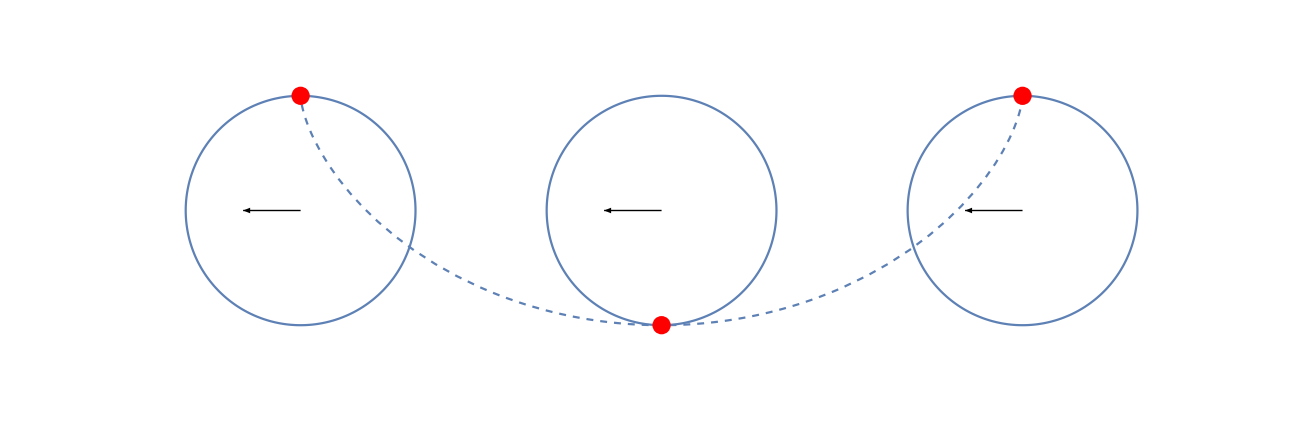

```mathematica
Show[ParametricPlot[{-t+Sin[t], -1+Cos[t] },{t,0,2*Pi}, PlotRange->{{-2.5*Pi, 1.5},{-2.5,0.5}}, Axes->False, PlotStyle->Dashed], ParametricPlot[{Cos[t]-Pi,Sin[t]-1},{t,0,2*Pi}], ParametricPlot[{Cos[t]-0,Sin[t]-1},{t,0,2*Pi}]
, ParametricPlot[{Cos[t]-2Pi,Sin[t]-1},{t,0,2*Pi}], Graphics[{PointSize[0.01],Red,Point[{0,0}]}], Graphics[{PointSize[0.01],Red,Point[{-Pi,-2}]}], Graphics[{PointSize[0.01],Red,Point[{-2Pi,0}]}], Graphics[{Arrowheads[0.02],Arrow[{{0,-1},{-0.5,-1}}]}], Graphics[{Arrowheads[0.02],Arrow[{{-Pi,-1},{-0.5-Pi,-1}}]}], Graphics[{Arrowheads[0.02],Arrow[{{0-2Pi,-1},{-0.5-2Pi,-1}}]}]]
```

```mathematica
D[ l^(-5)/(E^(A/l) - 1), l]
```

(A ⅇ^(A/l))/((-1+ⅇ^(A/l))^2 l^7)-5/((-1+ⅇ^(A/l)) l^6)

```mathematica
FindRoot[e*E^e/(E^e-1) - 5,{e,5}]
```

{e→4.96511}

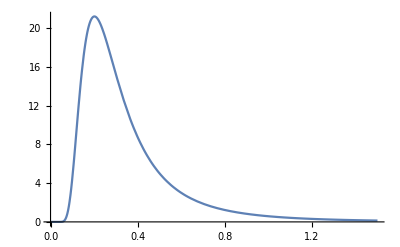

```mathematica
Plot[x^-5/(E^(1/x)-1),{x,0,1.5}, PlotRange-> Full]
```

```mathematica
N[Integrate[x^(3/2)/(E^x-1),{x,0,100}]]
```

1.78329

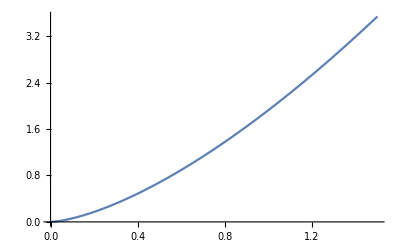

```mathematica
Plot[1.9259*x^(3/2),{x,0,1.5}]
```